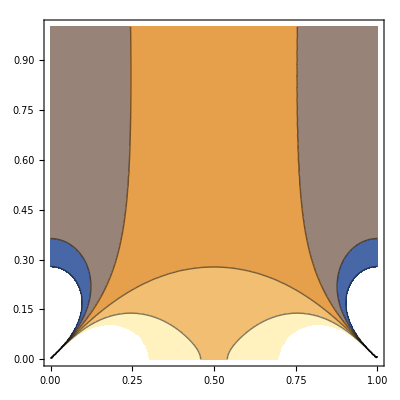

```mathematica
cutoff= 0.001;
ContourPlot[Re[PolyGamma[1,1-t + cutoff -I x]+PolyGamma[1,t + cutoff-I x]],{t,0,1},{x,0,1}]
```

```mathematica
r = 0.4;
FindRoot[Re[PolyGamma[1,1-t + cutoff -I r]+PolyGamma[1,t + cutoff -I r]], {t, 0.1}]
```

{t→0.223355}

```mathematica
FullSimplify[Together[1/(omcB + I*rBv + tauB + k)^2 + 1/(omcB + I*rBv - tauB + k)^2 +1/(omcB - I*rBv + tauB + k)^2 +1/(omcB - I*rBv - tauB + k)^2 ]]
```

(4 ((k+omcB-rBv) (k+omcB+rBv) ((k+omcB)^2+rBv^2)^2-((k+omcB)^4+10 (k+omcB)^2 rBv^2+rBv^4) tauB^2-(k+omcB-rBv) (k+omcB+rBv) tauB^4+tauB^6))/((((k+omcB)^2+rBv^2)^2-2 (k+omcB-rBv) (k+omcB+rBv) tauB^2+tauB^4)^2)